# Emirp Primes

An   emirp   (prime spelled backwards)   is a prime that when reversed   (in their decimal representation)   is a different prime.

## Tasks

Show the first twenty emirps

show all emirps between 7,700 and 8,000

show the 10,000th emirp

## The code

```mathematica
FindNEmirps[n_Integer]:=Module[{i=0,prime=2},
Reap[
While[i<n,
If[#1!=#2&&PrimeQ[#2]
,Sow[#1];i++
]&@@{prime,IntegerReverse[prime]}
;prime=NextPrime[prime]
]
]][[2,1]]
```

```mathematica
FindNEmirps[20]
```

{13,17,31,37,71,73,79,97,107,113,149,157,167,179,199,311,337,347,359,389}

```mathematica
FindEmirpsRange[{a_Integer,b_Integer}]:=Select[Range[a,b]
,If[PrimeQ[#]
,(#1!=#2&&PrimeQ[#2]&@@{#,IntegerReverse[#]})
,False]&
]
```

```mathematica
FindEmirpsRange[{7700,8000}]
```

{7717,7757,7817,7841,7867,7879,7901,7927,7949,7951,7963}

```mathematica
FindNthEmirps[n_Integer]:=Last@FindNEmirps[n]
```

```mathematica
FindNthEmirps[10000]
```

948349

# Leonardo numbers

The   Leonardo numbers   are a sequence of numbers defined by:

```mathematica
Leonardo[0]:=1
Leonardo[1]:=1
Leonardo[n_Integer]:=Leonardo[n-1]+Leonardo[n-2]+1
```

## Task

show the 1st   25   Leonardo numbers, starting at L(0).

allow the first two Leonardo numbers to be specified   [for L(0) and L(1)].

allow the   add   number to be specified   (1 is the default).

show the 1st   25   Leonardo numbers, specifying 0 and 1 for L(0) and L(1), and 0 for the add number.

## Code

### First Task

Let’s just modify the above function to give us the next Leonardo number.

```mathematica
Leonardo[{prev1_Integer,prev2_Integer}]:={prev2,prev1+prev2+1}
```

```mathematica
Leonardo[{n_Integer}]:=NestList[Leonardo[#]&,{1,1},n][[All,1]]
```

```mathematica
Leonardo[{25}]
```

{1,1,3,5,9,15,25,41,67,109,177,287,465,753,1219,1973,3193,5167,8361,13529,21891,35421,57313,92735,150049,242785}

### Second Task On

```mathematica
LeonardoCustom[n_Integer,{{zero_,one_},add_}]:=Which[
n==0,zero
,n==1,one
,True,Last@Nest[{#2,#2+#1+add}&@@#&,{zero,one},n-1]
]
```

```mathematica
LeonardoCustom[25,{{0,1},0}]
```

75025

```mathematica
LeonardoCustom[{n_Integer},{{zero_,one_},add_}]:=Which[
n==1,{zero}
,n==2,{zero,one}
,True,NestList[{#2,#2+#1+add}&@@#&,{zero,one},n-1][[All,1]]
]
```

```mathematica
LeonardoCustom[{25},{{0,1},0}]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368}

# Heronian Triangles

Heron’s formula for the area of a triangle given the length of its three sides a, b, and c is given by

A=√(s(s-a)(s-b)(s-c)),

where s is half the perimeter of the triangle, that is

s=(a+b+c)/2.

Heronian triangles are triangles whose sides and area are all integers.

An example is the triangle with sides 3,4,5 whose area is 6.

Define a Primitive Heronian Triangle as a Heronian triangle where the GCD of all three sides is 1.

## Tasks

Create a named function/method/procedure/... that implements Heron’s formula

Use the function to generate all the primitive Heronian triangles with sides <=200.

Show the count of how many triangles are found.

Order the triangles by first increasing area, then by increasing perimeter, then by increasing maximum side lengths

Show the first ten ordered triangles in a table of sides, perimeter, and area.

Show a similar ordered table for those triangles with area = 210

## The code

### First task

```mathematica
HeronArea[a_,b_,c_]:=With[{s=(a+b+c)/2}
,√(s(s-a)(s-b)(s-c))
]
```

```mathematica
HeronArea@@{16,17,17}
```

120

### Second task

```mathematica
PrimitiveTriangles[n_Integer]:=With[{HeronianQ=IntegerQ@*HeronArea} ,
Select[Tuples[Range[1,n],{3}]
,OrderedQ[#]
&&Apply[#1+#2>#3&,#]
&&Apply[GCD,#]==1
&&HeronianQ@@#&]]
```

### Third task

```mathematica
try=PrimitiveTriangles[200];
Length@try
```

517

### Fourth task

```mathematica
sortedtry=SortBy[try,{HeronArea@@#&,Total[#]/2&,Max[#]&}];
```

### Fifth task

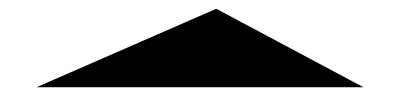
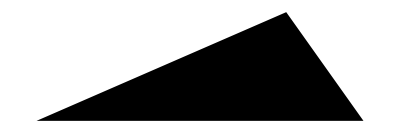
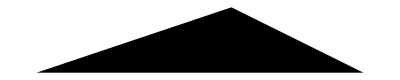
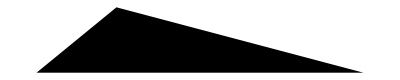
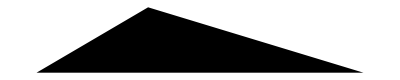
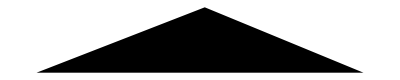
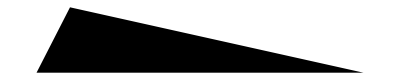
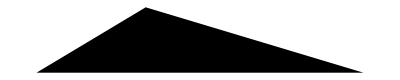
Sides | Area | Perimeter | Max Side | 
{3,4,5} | 6 | 6 | 5 | -Graphics-
{5,5,6} | 12 | 8 | 6 | -Graphics-
{5,5,8} | 12 | 9 | 8 | -Graphics-
{4,13,15} | 24 | 16 | 15 | -Graphics-
{5,12,13} | 30 | 15 | 13 | -Graphics-
{9,10,17} | 36 | 18 | 17 | -Graphics-
{3,25,26} | 36 | 27 | 26 | -Graphics-
{7,15,20} | 42 | 21 | 20 | -Graphics-
{10,13,13} | 60 | 18 | 13 | -Graphics-
{8,15,17} | 60 | 20 | 17 | -Graphics-

```mathematica
first10=Take[sortedtry,10];
Grid[Join[
{{"Sides","Area","Perimeter","Max Side"}},
{#,HeronArea@@#,Total[#]/2,Max[#],
Graphics@Triangle[{{0,0},{Last@#,0},{√((First@#)^2-((HeronArea@@#)/(Last@#))^2),((HeronArea@@#)/(Last@#))}}]
}&/@first10]
]
```

### Sixth task

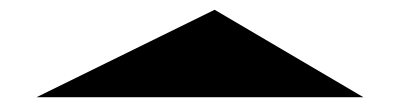
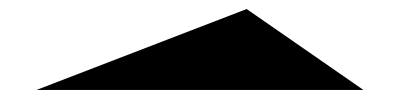
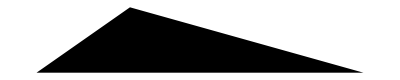
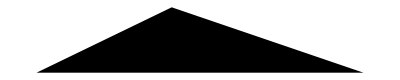
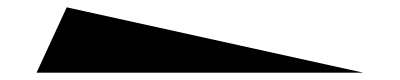
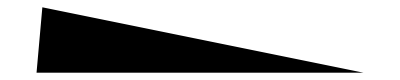
Sides | Area | Perimeter | Max Side | 
{17,25,28} | 210 | 35 | 28 | -Graphics-
{20,21,29} | 210 | 35 | 29 | -Graphics-
{12,35,37} | 210 | 42 | 37 | -Graphics-
{17,28,39} | 210 | 42 | 39 | -Graphics-
{7,65,68} | 210 | 70 | 68 | -Graphics-
{3,148,149} | 210 | 150 | 149 | -Graphics-

```mathematica
try210=Select[try,210==HeronArea@@#&];
sortedtry210=SortBy[try210,{Total[#]/2&,Max[#]&}];
Grid[Join[
{{"Sides","Area","Perimeter","Max Side"}},
{#,HeronArea@@#,Total[#]/2,Max[#],
Graphics@Triangle[{{0,0},{Last@#,0},{√((First@#)^2-(210/(Last@#))^2),(210/(Last@#))}}]
}&/@sortedtry210]
]
```